```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@AbsoluteOptions[g,PlotRange],Sequence@@Options[g,Epilog]]
```

/home/zack/cantera/ratematrix

data/test

{1000.,53,325,1500,1,0.003}

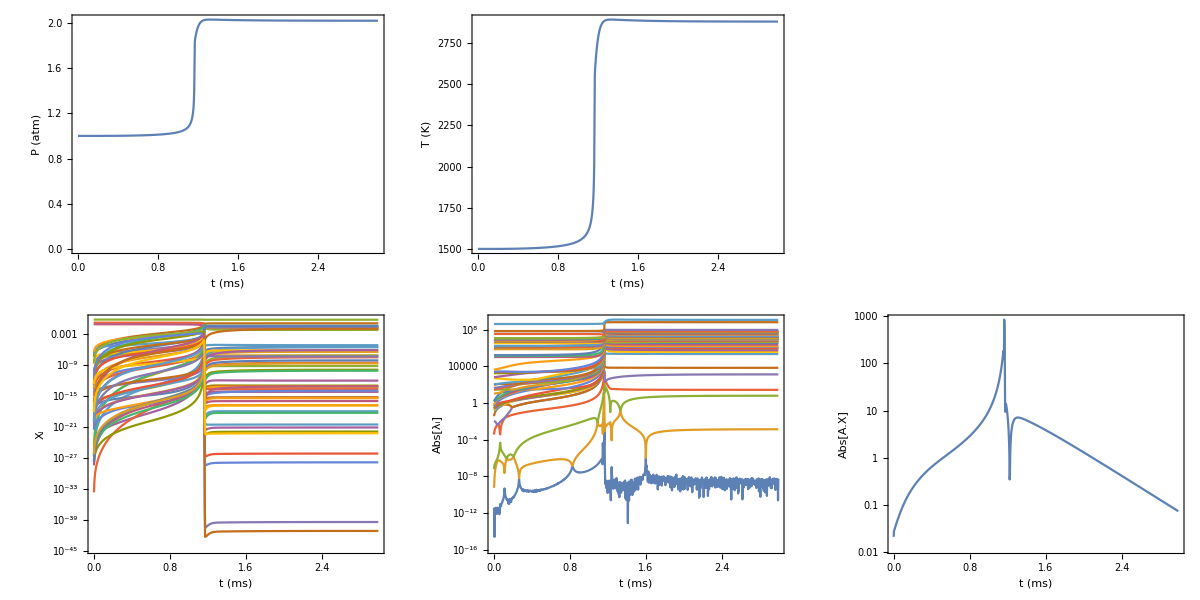

plots/quasilinear2.pdf

```mathematica
filebase="data/test"
dat=Import[filebase<>"out.dat"];
{Nt,ns,nr,T,P,tmax}=dat[[1]]
A=Partition[Partition[BinaryReadList[filebase<>"matrices.npy","Real64"][[17;;-1]],ns],ns];
evals=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2],ns];
evecs=Partition[Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],ns],ns];
concentrations=Partition[BinaryReadList[filebase<>"concentrations.npy","Real64"][[17;;-1]],Round[Nt]];
p=Grid[{{ListPlot[Transpose[{dat[[3]]/10^-3,dat[[5]]}],Frame->True, Axes->False,FrameStyle->Directive[AbsoluteThickness[2.0],Black],LabelStyle->Directive[16,Black],FrameLabel->{"t (ms)", "P (atm)"}, ImageSize->300, Joined->True,PlotRange->All,ImagePadding->{{75,15},{75,55}},AspectRatio->1],ListPlot[Transpose[{dat[[3]]/10^-3,dat[[4]]}],Frame->True, Axes->False,FrameStyle->Directive[AbsoluteThickness[2.0],Black],LabelStyle->Directive[16,Black],FrameLabel->{"t (ms)", "T (K)"}, ImageSize->300, Joined->True,PlotRange->All,ImagePadding->{{75,15},{75,55}},AspectRatio->1],rasterizeBackground[MatrixPlot[A[[-1]],FrameTicks->{{Table[{i,i},{i,1,ns,Floor[ns/5]}],Table[{i,""},{i,1,ns,Floor[ns/5]}]},{Table[{i,i},{i,1,ns,Floor[ns/5]}],Table[{i,""},{i,1,ns,Floor[ns/5]}]}},DataReversed->{True,False},FrameLabel->{{i,"Final rate matrix A"},{j,None}},FrameStyle->Directive[AbsoluteThickness[2.0],Black],LabelStyle->Directive[16,Black], ImageSize->300,ImagePadding->{{75,15},{75,55}},AspectRatio->1],200]},{ListLogPlot[Transpose[{dat[[3]]/10^-3,#}]&/@concentrations,Frame->True, Axes->False,FrameStyle->Directive[AbsoluteThickness[2.0],Black],LabelStyle->Directive[16,Black],FrameLabel->{"t (ms)", Subscript[X,i]}, ImageSize->300, Joined->True,PlotRange->All,ImagePadding->{{75,15},{75,55}},AspectRatio->1],ListLogPlot[Transpose[{dat[[3,2;;-1]]/10^-3,#}]&/@Transpose[Abs[evals]][[2;;-1,2;;-1]],Frame->True, Axes->False,FrameStyle->Directive[AbsoluteThickness[2.0],Black],LabelStyle->Directive[16,Black],FrameLabel->{"t (ms)", Abs[Subscript[λ,i]]}, ImageSize->300, Joined->True,PlotRange->All,ImagePadding->{{75,15},{75,55}},AspectRatio->1],ListLogPlot[Transpose[{dat[[3]]/10^-3,#}]&@Table[Abs[concentrations[[All,m]].A[[m]].concentrations[[All,m]]],{m,1,Length[A]}],PlotRange->All,Joined->True,Frame->True, Axes->False,FrameStyle->Directive[AbsoluteThickness[2.0],Black],LabelStyle->Directive[16,Black],FrameLabel->{"t (ms)", Abs[Dot["A","X"]]}, ImageSize->300,ImagePadding->{{75,15},{75,55}},AspectRatio->1]}}]
Export["plots/quasilinear2.pdf",p]
```

```mathematica
If[!DirectoryQ["animation"],CreateDirectory["animation"];]
max=Max[Abs[A]];
max=Mean[Cases[Flatten[Abs[A]],u_/;u>0]];
Monitor[plots=Table[MatrixPlot[A[[m]],ColorFunction->(ColorData["TemperatureMap"][(#+max)/(2*max)]&),ColorFunctionScaling->False,FrameTicks->{{Table[{i,i},{i,1,ns,Floor[ns/5]}],Table[{i,""},{i,1,ns,Floor[ns/5]}]},{Table[{i,i},{i,1,ns,Floor[ns/5]}],Table[{i,""},{i,1,ns,Floor[ns/5]}]}},DataReversed->{True,False},LabelStyle->Directive[16,Black],FrameLabel->{{i,Subscript["A","i j"]},{j,None}},ImageSize->350],{m,1,Length[A],1}];,m]
Manipulate[plots[[m]],{m,1,Length[plots],1}]
Monitor[Do[Export["animation/"<>IntegerString[m-1,10,4]<>".png",plots[[m]]];,{m,1,Length[plots]}],m]
```